f(x_1,x_2)= 3 x_2 - x_1->max
-2 x_1 + x_2 + y_1= 2
5 x_1 + 4 x_2 +y_2 = 30
-x_1 + x_2 +y_3 = 3
x_1 >= 0,x_2>= 0

начальное  базисное  решение: x

```mathematica
Manipulate[Show[ContourPlot[x -3y == z,{x,0,10},{y,0,10}],RegionPlot[Callout[{2x- y≥ -2 && 5x+ 4y ≤ 30 &&-x+y ≤ 3}, "restrictions", {5,1}],{x,0,10},{y,0,10}, BoundaryStyle->Directive[Thickness[Medium],Dashed]]], {{z,-13},0,- 20},ControlPlacement -> Top]
```

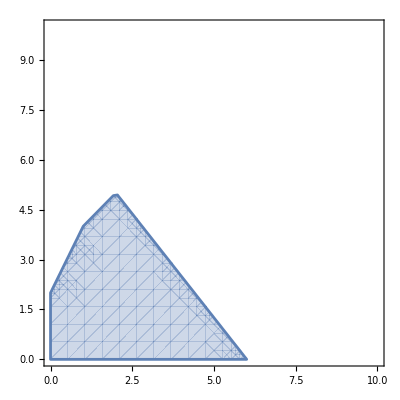

```mathematica
RegionPlot[{-2 x + y<=2 && 5x+ 4y ≤ 30 &&-x+y ≤ 3},{x,0,10},{y,0,10}]
```

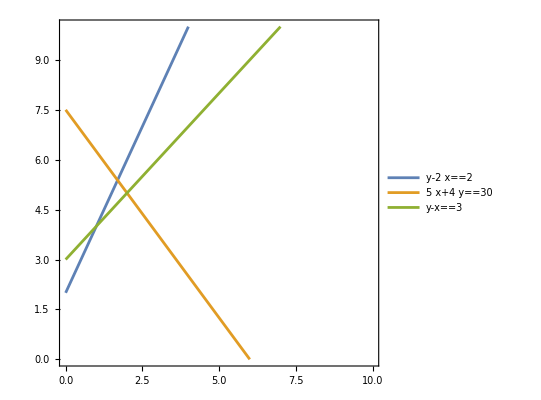

```mathematica
ContourPlot[{-2 x + y==2 ,5x+ 4y == 30 ,-x+y == 3},{x,0,10},{y,0,10}, PlotLegends->"Expressions"]
```